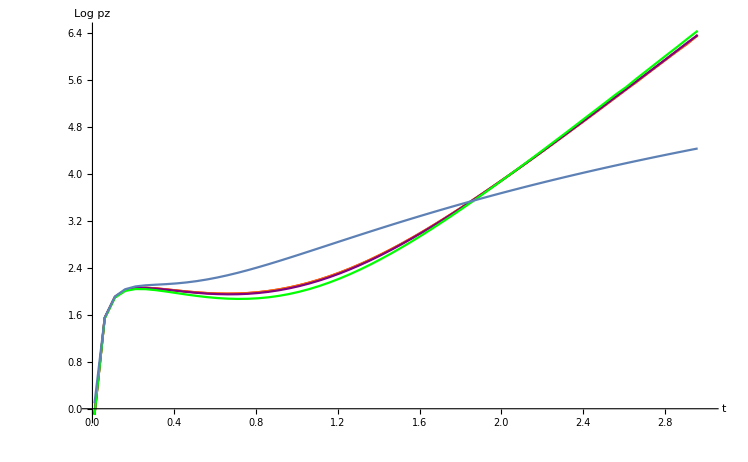

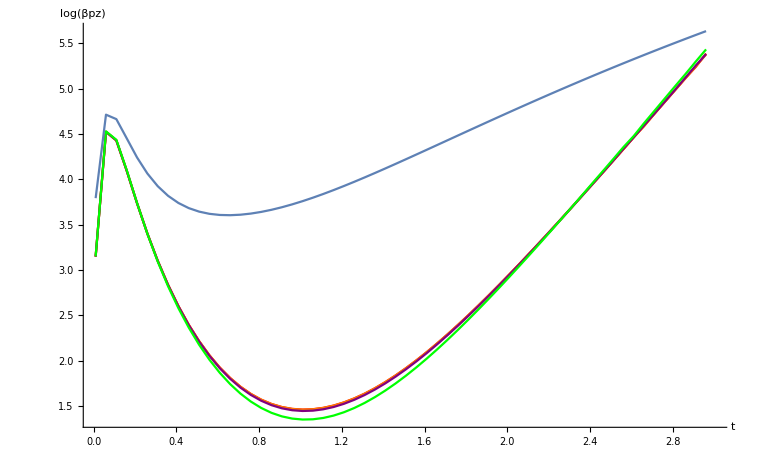

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz,
fRNAdS,qcritRNAdS,zm1RNAdS,zmRNAdS,pzRNAdS,βpzRNAdS,dfz2
},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
fRNAdS[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcritRNAdS[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1RNAdS[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,4},Method->"ExplicitRungeKutta"
];
zmRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=zm1RNAdS[q1,μ1,zh1,zs1][t1];
dfz2[t_,q1_,μ1_,zh1_,zs1_]:=D[zmRNAdS[t1,q1,μ1,zh1,zs1],t1]/.{t1->t};
pzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz,β},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
β=1/(D[fRNAdS[zh1,μ1,zw],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3]],0.1,0,0.01,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3]],0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[pzRNAdS[i,0.8*qcritRNAdS[Sqrt[3],1,0.1],Sqrt[3],1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log pz}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3] ],0.1,0,0.01,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3] ],0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[βpzRNAdS[i,0.8*qcritRNAdS[Sqrt[3],1,0.1],Sqrt[3],1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log[βpz]}
]];
]
```

```mathematica
Hypergeometric2F1[1/4,1/2,5/4,0]
```

1

```mathematica
Series[(μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- (-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2])z^3+1-β^2 z^2/2),{γ,0,1},{β,0,1}]
```

((1-z^3-(z^3 μ^2)/4+(z^4 μ^2)/4)+O[β]^2)+1/80 (z^3 μ^4-z^8 μ^4) γ+O[γ]^2

```mathematica
0.75Sqrt[1/γ((1+(6-β^2)γ)^2-1)]/.{β->0.8,γ->2}
```

6.1928

```mathematica
Series[(μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- (-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2])z^3+1-β^2 z^2/2)/.{β->0},{γ,0,1}]
```

1/4 (4-4 z^3-z^3 μ^2+z^4 μ^2)+1/80 (z^3 μ^4-z^8 μ^4) γ+O[γ]^2

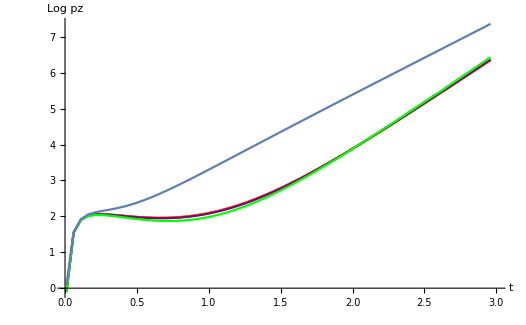

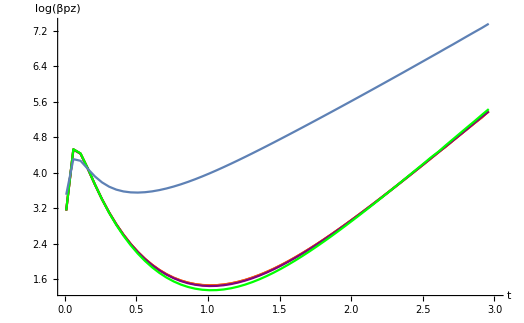

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz,
fRNAdS,qcritRNAdS,zm1RNAdS,zmRNAdS,pzRNAdS,βpzRNAdS,dfz2
},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
fRNAdS[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcritRNAdS[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1RNAdS[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,4},Method->"ExplicitRungeKutta"
];
zmRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=zm1RNAdS[q1,μ1,zh1,zs1][t1];
dfz2[t_,q1_,μ1_,zh1_,zs1_]:=D[zmRNAdS[t1,q1,μ1,zh1,zs1],t1]/.{t1->t};
pzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz,β},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
β=1/(D[fRNAdS[zh1,μ1,zw],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3]],0.1,0,0.01,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3]],0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[pzRNAdS[i,0.8*qcritRNAdS[2.5,1,0.1],2.5,1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log pz}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.001,2/Sqrt[3] ],0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.01,2/Sqrt[3] ],0.1,0,0.01,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,0.1,2/Sqrt[3] ],0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[βpz[i,0.8qcrit[0.1,0,1,2/Sqrt[3]],0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[βpzRNAdS[i,0.8*qcritRNAdS[2.5,1,0.1],2.5,1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log[βpz]}
]];
]
```

```mathematica
Block[
{qcrit,m,f,qcritRNAdS},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
qcritRNAdS[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
Print[qcrit[0.1,0,0.001,2/Sqrt[3] ]];
Print[qcritRNAdS[2.5,1,0.1]];
]
```

9.61767

4.4297

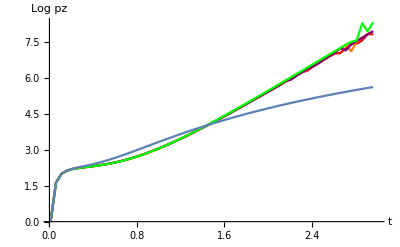

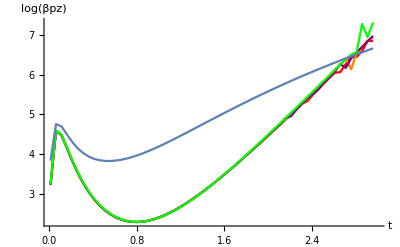

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz,βpz,
fRNAdS,qcritRNAdS,zm1RNAdS,zmRNAdS,pzRNAdS,βpzRNAdS,dfz2
},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,4}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz,β,n1,zw},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
β=1/(D[f[zw,β1,γ1,μ1],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
fRNAdS[zh_,μ_,z_]:=1-(1+zh^2μ^2)(z/zh)^3+zh^2μ^2(z/zh)^4;
qcritRNAdS[μ_,zh_,zs_]:=zh Sqrt[1-(1+zh^2 μ^2)(zs/zh)^3+zh^2μ^2(zs/zh)^4]/μ/zs/(zh-zs);
zm1RNAdS[q1_,μ1_,zh1_,zs1_]:=NDSolveValue[
{-(q μ)/zh-(zh^3 z[t] (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+z'[t]^2/(z[t]^2 (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))-(z[t] (-3 (1+zh^2 μ^2)+4 zh μ^2 z[t]-(zh^6 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)))/(2 zh^3 √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(√(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/z[t]^2-z''[t]/((z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) √(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))+(z'[t]^2 (-(3 (1+zh^2 μ^2) z[t]^2)/zh^3+(4 μ^2 z[t]^3)/zh^2-(zh^3 z[t]^2 (3+3 zh^2 μ^2-4 zh μ^2 z[t]) z'[t]^2)/((zh-z[t])^2 (zh^2+zh z[t]+z[t]^2-zh μ^2 z[t]^3)^2)-(2 z''[t])/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2)))/(2 (z[t]-((1+zh^2 μ^2) z[t]^4)/zh^3+(μ^2 z[t]^5)/zh^2) (1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2-z'[t]^2/(1-((1+zh^2 μ^2) z[t]^3)/zh^3+(μ^2 z[t]^4)/zh^2))^(3/2))==0/.{μ->μ1,zh->zh1,q->q1},z[0]==zs1,z'[0]==0},z,{t,0.01,4},Method->"ExplicitRungeKutta"
];
zmRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=zm1RNAdS[q1,μ1,zh1,zs1][t1];
dfz2[t_,q1_,μ1_,zh1_,zs1_]:=D[zmRNAdS[t1,q1,μ1,zh1,zs1],t1]/.{t1->t};
pzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
βpzRNAdS[t1_,q1_,μ1_,zh1_,zs1_]:=Block[
{zd,z2,fz,β},
z2=zmRNAdS[t1,q1,μ1,zh1,zs1];
fz=fRNAdS[zh1,μ1,z2];
zd=dfz2[t1,q1,μ1,zh1,zs1];
β=1/(D[fRNAdS[zh1,μ1,zw],zw]/.{zw-> z2});
Return[β/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Print[Show[
ListLinePlot[Table[{i,Abs[pz[i,1,0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1,0,0.01,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[pz[i,1,0.1,0,1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[pzRNAdS[i,1,Sqrt[3],1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log pz}
]];
Print[Show[
ListLinePlot[Table[{i,Abs[βpz[i,1,0.1,0,0.001,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[βpz[i,1,0.1,0,0.01,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[βpz[i,1,0.1,0,0.1,2/Sqrt[3] ]]//Log},{i,0.01,3,0.05}],PlotStyle->Purple],
ListLinePlot[Table[{i,Abs[βpz[i,1,0.1,0,1,2/Sqrt[3]]]//Log},{i,0.01,3,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Log[βpzRNAdS[i,1,Sqrt[3],1,0.1]]//Abs},{i,0.01,3,0.05}]],
PlotRange->{{0.01,3},All},AxesOrigin->{0,0},AxesLabel->{t,Log[βpz]}
]];
]
```